```mathematica
ResourceFunction["MaTeXInstall"][];
ConfigureMaTeX["Ghostscript"->"C:\\Program Files\\gs\\gs10.03.0\\bin\\gswin64c.exe"];
ConfigureMaTeX["pdfLaTeX" -> "C:\\texlive\\2024\\bin\\windows\\pdflatex.exe"];
<<MaTeX`;
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor}\\usepackage{amsmath}"}]

MaTeX["x^2"] (*Este bloque echa a andar MaTeX. Para tener tipografia tipo LaTeX*)
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor}\usepackage{amsmath}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

-Graphics-

```mathematica
BoltzmannConstant=1.380649*10^-23;(*J/K*)
PlanckConstant = 6.626068*10^-34/2π;(*Js*)
densidad  = 5.317*1/1000*100/1*100/1*100/1;(*Kg*m^-3*)
YoungModule=8.59*10^-5/1*100/1*100/1*100/1;(*N*m^-3*)
ν=1/3;
velocidad=4*10^5*1/100;
altura=200*10^-9;
ancho = 300*10^-9;
largo = 10*10^-6;
rigidez=YoungModule*altura^3/(12*(1-ν^3));
ωRing=(√(rigidez/(densidad*altura)))/ancho^2;
a = 0.01; (*medido en unidades de W*)
aPrime = 0.01;(*medido en unidades de W*)
```

```mathematica
coeficienteB[ω_, k_]:=((ω+(1-ν)k^2)Cosh[(√(ω+k^2))/2])/((ω-(1-ν)k^2)Cos[(√(ω-k^2))/2])*a;
coeficienteBPrima[ω_, k_]:=((ω+(1-ν)k^2)Sinh[(√(ω+k^2))/2])/((ω-(1-ν)k^2)Sin[(√(ω-k^2))/2])*aPrime;
```

```mathematica
frecuenciaωSimPositivo[waveNumber_, offset_]:= Re[w/.First[With[{k=waveNumber}, FindRoot[Sqrt[w-k^2]*(w+(1-ν)k^2)^2 *Cosh[Sqrt[w+k^2]/2]*Sin[Sqrt[w-k^2]/2]+
Sqrt[w+k^2]*(w-(1-ν)k^2)^2 *Sinh[Sqrt[w+k^2]/2]*Cos[Sqrt[w-k^2]/2]==0,{w,Abs[k]^2+offset}, WorkingPrecision->20]]]];
```

```mathematica
antisimetrica=ContourPlot[Sqrt[Abs[w]+k^2]*(Abs[w]-(1-ν)k^2)^(2) *Cosh[Sqrt[Abs[w]+k^2]/2]*Sin[Sqrt[Abs[w]-k^2]/2]-
Sqrt[Abs[w]-k^2]*(Abs[w]+(1-ν)k^2)^(2) *Sinh[Sqrt[Abs[w]+k^2]/2]*Cos[Sqrt[Abs[w]-k^2]/2]==0,{k,-20,20},{w,-300,300}, PlotTheme->"Monochrome", MaxRecursion->5,  ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-300,300,100]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,10]}] (*x axis*),None}
}];
puntosAntiSimetrica = Flatten[Cases[Normal@antisimetrica,Line[x_]:>x,Infinity],1];
puntosAntiSimetrica60=Cases[puntosAntiSimetrica,x_/;Abs[x[[2]]-60-x[[1]]^2]<20 ];
frecuenciaωAntiSimPositivo=Interpolation[puntosAntiSimetrica60];
frecuenciaωAntiSimPositivo[0]*ωRing
```

5.12447×10^6

```mathematica
frecuenciaωAntiSimPositivo[5]
```

93.6519

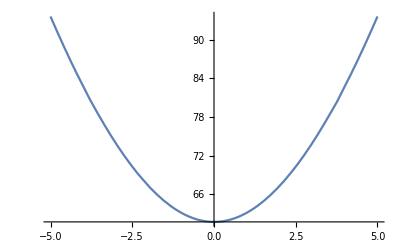

```mathematica
Plot[frecuenciaωAntiSimPositivo[x], {x, -5,5}]
```

```mathematica
amplitudWSim[k_,y_,off_]:=Re[(a*Cosh[√(ω+k^2)y]+b*Cos[(√(ω-k^2))*y])/Sqrt[0.5* (a^2+b^2+1/ω 4* a* b √(-k^2+ω) Cosh[(√(k^2+ω))/2] Sin[1/2 √(-k^2+ω)]+(b^2 Sin[√(-k^2+ω)])/(√(-k^2+ω))+1/(√(k^2+ω))a*(1/ω 4b*(k^2+ω) Cos[1/2 √(-k^2+ω)] Sinh[(√(k^2+ω))/2]+a*Sinh[√(k^2+ω)]))]/.{b->coeficienteB[frecuenciaωSimPositivo[k, off],k], ω->frecuenciaωSimPositivo[k, off]}];
amplitudWAntiSim[k_,y_]:=(aPrime*Sinh[(√(ω+k^2))*y]+bPrime*Sin[(√(ω-k^2))*y])/(√(1/2 (-aPrime^2+bPrime^2+(4 aPrime bPrime √(k^2+ω) Cosh[(√(k^2+ω))/2] Sin[1/2 √(-k^2+ω)])/ω-(bPrime^2 Sin[√(-k^2+ω)])/(√(-k^2+ω))-(4 aPrime bPrime √(-k^2+ω) Cos[1/2 √(-k^2+ω)] Sinh[(√(k^2+ω))/2])/ω+(aPrime^2 Sinh[√(k^2+ω)])/(√(k^2+ω)))))/.{bPrime->coeficienteBPrima[frecuenciaωAntiSimPositivo[k],k], ω->frecuenciaωAntiSimPositivo[k]};
```

```mathematica
amplitudWSim[5, 0.5,0]
NIntegrate[amplitudWSim[2,y,0]^2,{y, -0.5,0.5}]
```

1.17303

1.

```mathematica
distribucionBE[frecuencia_,temp_] := 1/(Exp[(PlanckConstant*frecuencia)/(BoltzmannConstant*temp)]-1);
distribucionMB[frecuencia_, temp_]:=1/Exp[(PlanckConstant*frecuencia)/(BoltzmannConstant*temp)];
BE[x_] := 1/(Exp[x]-1);
MB[x_]:=1/Exp[x];
```

```mathematica
PlanckConstant*frecuenciaωSimPositivo[2*π*30*ancho/largo, 0]*ωRing
```

2.71294×10^-27

```mathematica
BoltzmannConstant*1
```

1.38065×10^-23

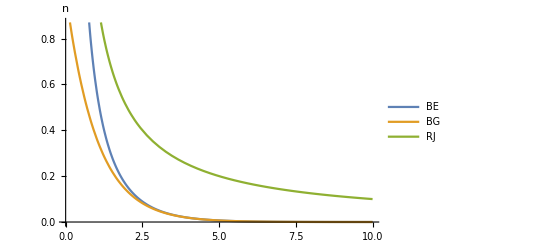

```mathematica
comparaDistros = Plot[{BE[x],MB[x],1/x},{x, 0,10}, PlotLegends->{BE, BG, RJ}, AxesLabel->{MaTeX["\\hbar\\omega/k_{B}T"],"n"}]
```

```mathematica
Export["compareDistributions.pdf", comparaDistros]
```

compareDistributions.pdf

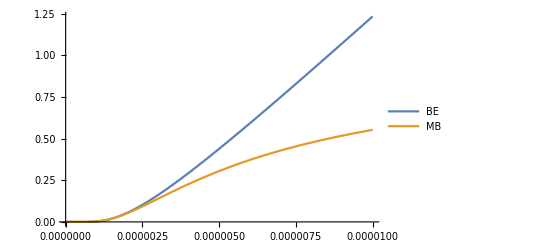

```mathematica
Plot[{distribucionBE[frecuenciaωSimPositivo[1, 0]*ωRing,t], distribucionMB[frecuenciaωSimPositivo[1,0]*ωRing, t]}, {t, 0,0.00001}, PlotLegends->{BE,MB}]
```

```mathematica
temperatura=PlanckConstant*velocidad/(BoltzmannConstant*ancho)
```

1.00515

```mathematica
meanSquaredDisplacementBE[y_,θ1_,θ2_]:=PlanckConstant/(densidad*largo*ancho*altura)*Sum[(amplitudWSim[2π*n*ancho/largo,y,0.0]^2/(frecuenciaωSimPositivo[2π*n*ancho/largo, 0.0]*ωRing))*(distribucionBE[frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing,θ1] +distribucionBE[frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing,θ2] +2),{n,1, 30}];(*<ξ^2>*)



meanSquaredDisplacementAntiBE[y_,θ1_,θ2_]:=Sum[PlanckConstant/(densidad*largo*ancho*altura)*(amplitudWAntiSim[2π*n*ancho/largo,y]^2/(frecuenciaωAntiSimPositivo[2π*n*ancho/largo]*ωRing))*(distribucionBE[frecuenciaωAntiSimPositivo[2π*n*ancho/largo]*ωRing,θ1] +distribucionBE[frecuenciaωAntiSimPositivo[2π*n*ancho/largo]*ωRing,θ2] +2),{n,1, 30}];
```

```mathematica
meanSquaredDisplacementBE[0.5,11, 10.9]
```

1.32682×10^-14

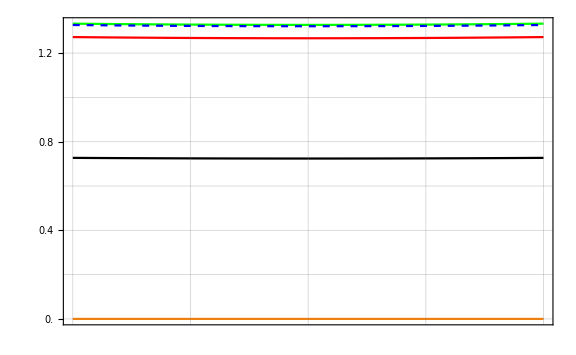

```mathematica
msdSimBE=Plot[{ meanSquaredDisplacementBE[y,11.0,10.99995],meanSquaredDisplacementBE[y,11.0,10.9],meanSquaredDisplacementBE[y,11.0, 10.0], meanSquaredDisplacementBE[y,11.0,1.0],meanSquaredDisplacementBE[y, 1*10^-4, 5*10^-5]},{y, -0.5,0.5},PlotRange->Full,  PlotStyle->{Green,Directive[Blue, Dashed], Red, Black, Orange}, ImageSize->Large, GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->18}, Frame->True,FrameStyle->Directive[Black, Thick],
FrameLabel->{{MaTeX["\\left\\langle \\hat{\\xi}^{2} \\right\\rangle (\\times 10^{-14} \\mathrm{m}^{2})", Magnification->1.8], None},{
None, None}
},
FrameTicks->{
{Table[{j*10^-14,Style[ToString[j], Black]},{j,Range[0,2,0.2]}], False(* y axis*)},{Table[{j, ""},{j,Range[-0.5,0.5,0.25]}](*x axis*),False}
}]
```

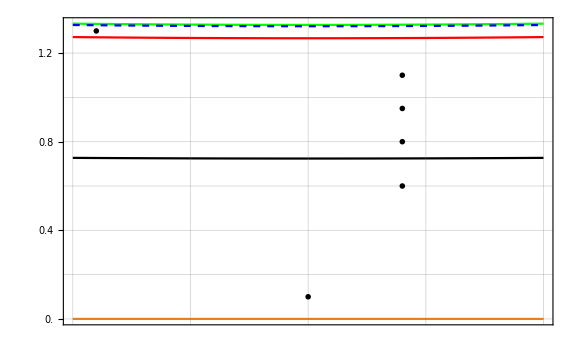

```mathematica
msdSimBEAnotada=Show[msdSimBE,Epilog->{Inset[Style[MaTeX["\\color{green}\\Delta T = 5\\times 10^{-5} \\mathrm{K}", Magnification->1.6], Green],{0.2,1.1*10^-14}],
Inset[MaTeX["\\color{blue}\\Delta T = 0.1 \\mathrm{K}", Magnification->1.6],{0.2,0.95*10^-14}],
Inset[MaTeX["\\color{red}\\Delta T = 1\\mathrm{K}", Magnification->1.6],{0.2,0.8*10^-14}],Inset[MaTeX["\\color{black}\\Delta T = 10 \\mathrm{K}", Magnification->1.6],{0.2,0.6*10^-14}],
Inset[MaTeX["\\color{orange} \\Delta T = 5 \\times 10^{-5} \\mathrm{K} (T_{1}= \\times 10^{-4} \\mathrm{K})", Magnification->1.5],{0.,0.1*10^-14}],
Inset[MaTeX["\\mathrm{a)}", Magnification->1.8 ],{-0.45,1.3*10^-14}]}]
```

```mathematica
meanSquaredDisplacementAntiBE[0.5,11.,10.9]
meanSquaredDisplacementAntiBE[0.5, 11., 1]
```

2.99951×10^-19

1.64359×10^-19

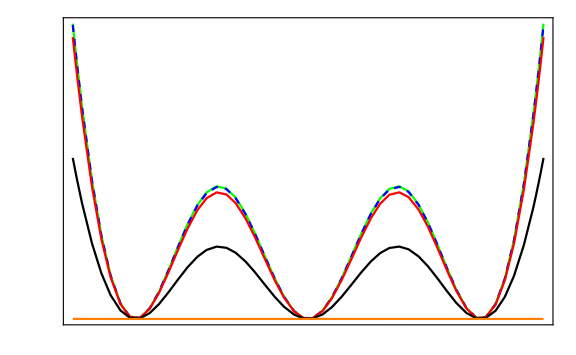

```mathematica
msdAntiSimBE=Plot[{meanSquaredDisplacementAntiBE[y,11.0,10.99995], meanSquaredDisplacementAntiBE[y,11.0,10.9],meanSquaredDisplacementAntiBE[y,11.0, 10.0], meanSquaredDisplacementAntiBE[y,11.0,1.0],meanSquaredDisplacementAntiBE[y, 1*10^-4, 5*10^-5]},{y, -0.5,0.5},PlotRange->Full,  PlotStyle->{Green,Directive[Blue, Dashed], Red, Black,Orange}, ImageSize->Large, GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->18}, Frame->True,FrameStyle->Directive[Black, Thick],
FrameLabel->{{ None,MaTeX["\\left\\langle \\hat{\\xi}^{2} \\right\\rangle (\\times 10^{-19} \\mathrm{m}^{2})", Magnification->1.8]},{
None, None}
}, FrameTicks->{
{Table[{j*10^-19,""},{j,Range[0,3,1]}],Table[{j*10^-19,Style[ToString[j], Black]},{j,Range[0,3,1]}](* y axis*)},{Table[{j,""},{j,Range[-0.5,0.5,0.25]}](*x axis*),False}
}]
```

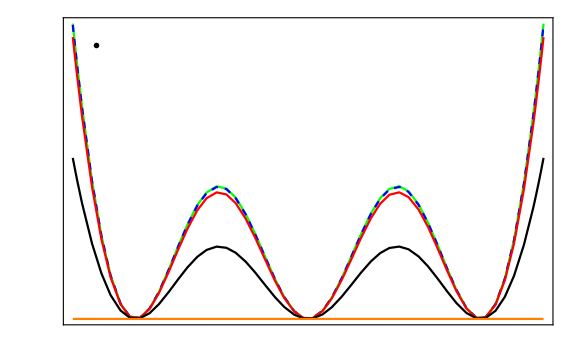

```mathematica
msdAntiSimBEAnotada=Show[msdAntiSimBE,GridLines->{{-0.5, -0.25,0,0.25, 0.5},Automatic},Epilog->{
Inset[MaTeX["\\mathrm{b)}", Magnification->1.8 ],{-0.45,2.8*10^-19}]}]
```

```mathematica
Export["differentTemperatures.pdf",msdSimBE]
```

differentTemperatures.pdf

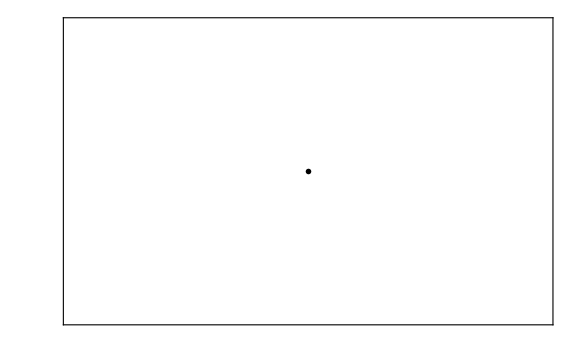

```mathematica
msdSimMB=Plot[{meanSquaredDisplacementMB[y], meanSquaredDisplacementAntiMB[y]},{y, -0.5,0.5},PlotRange->Full,  PlotStyle->{Blue, Red}, ImageSize->Large, GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->18}, Frame->True,FrameStyle->Directive[Black, Thick],
FrameLabel->{{None,MaTeX["\\left\\langle \\hat{\\xi}^{2} \\right\\rangle (\\times 10^{-21} \\mathrm{m}^{2})", Magnification->1.8]},{
None, None}
},
FrameTicks->{
{Table[{j*10^-21,""},{j,Range[0,5,2]}],Table[{j*10^-21,Style[ToString[j], Black]},{j,Range[0,5,2]}](* y axis*)},{Table[{j,""},{j,Range[-0.5,0.5,0.25]}](*x axis*),False}
},
Epilog->Inset[MaTeX["\\mathrm{b)}", Magnification->1.8],{-0.47,4.2*10^-21}]]
```

```mathematica
Export["msdMB.pdf",msdSimMB]
```

msdMB.pdf

```mathematica
meanSquaredDisplacementMB[0.5]
meanSquaredDisplacementMB[0.0]
```

meanSquaredDisplacementMB[0.5]

meanSquaredDisplacementMB[0.]

```mathematica
Export["meanQuadraticSymmetric.pdf",%]
```

meanQuadraticSymmetric.pdf

```mathematica
CorrienteBE[y_, θ1_,θ2_]:=Sum[(PlanckConstant*velocidad^2)/(largo*altura*ancho)*(2π*n/largo)*amplitudWSim[2π*n*ancho/largo,y,0.0]^2* (distribucionBE[frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing,θ1] -distribucionBE[frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing,θ2] ), {n, 1, 30}];
CorrienteAntiBE[y_, θ1_,θ2_]:=Sum[(PlanckConstant*velocidad^2)/(largo*altura*ancho)*(2π*n/largo)*amplitudWAntiSim[2π*n*ancho/largo,y]^2* (distribucionBE[frecuenciaωAntiSimPositivo[2π*n*ancho/largo]*ωRing,θ1] -distribucionBE[frecuenciaωAntiSimPositivo[2π*n*ancho/largo]*ωRing,θ2] ), {n, 1, 30}]
```

```mathematica
CorrienteBE[0.5,10.0,0.9]
```

3.27067×10^6

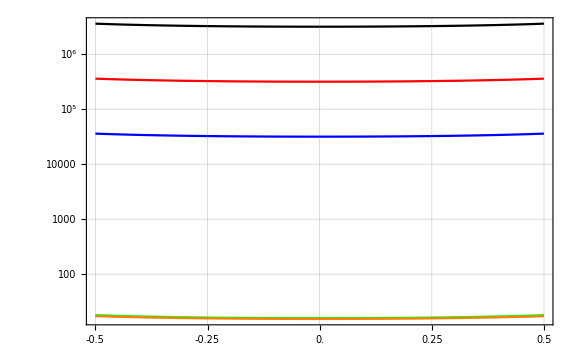

```mathematica
corrientePlotBE=LogPlot[{CorrienteBE[y, 11,10.99995],CorrienteBE[y, 11,10.9], CorrienteBE[y, 11,10.0],CorrienteBE[y, 11,1], CorrienteBE[y, 1*10^-4, 5*10^-5]},{y,-0.5,0.5}, PlotStyle->{Green,Blue, Red, Black, Orange}, ImageSize->Large, GridLines->Automatic, FrameTicks->{
{All, False(*y axis*)},{Table[{j,j},{j,Range[-0.5,0.5,0.25]}](*x axis*),False}
},MaxRecursion->1,
LabelStyle->{FontFamily->"CMU Serif", FontSize->18}, Frame->True,FrameStyle->Directive[Black, Thick]]
```

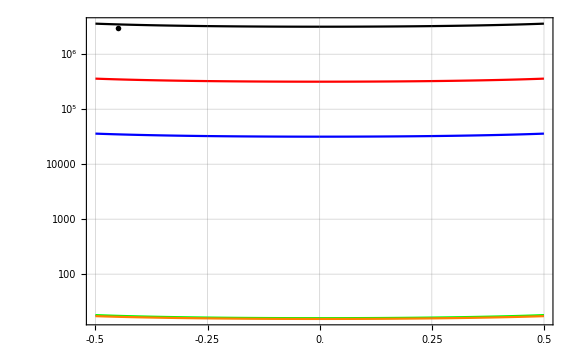

```mathematica
corrientePlotBEAnotada = Show[corrientePlotBE, 
FrameLabel->{{MaTeX["\\left\\langle \\hat{J} \\right\\rangle (\\mathrm{J}/\\mathrm{m}^{2}\\mathrm{s})", Magnification->1.8], None},{
MaTeX["y/W", Magnification->1.8], None}
},

Epilog->Inset[MaTeX["\\mathrm{e)}", Magnification->1.8],{-0.45,Log[3*10^6]}]]
```

```mathematica
CorrienteAntiBE[0.25, 11.,10.9]
```

2120.73

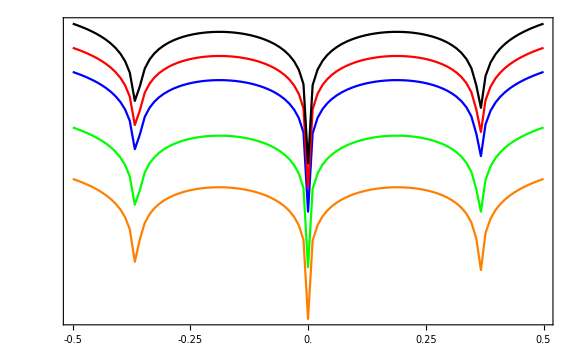

```mathematica
corrientePlotAntiBE=LogPlot[{CorrienteAntiBE[y, 11,10.9995],CorrienteAntiBE[y, 11,10.9], CorrienteAntiBE[y, 11,10.0],CorrienteAntiBE[y, 11,1],CorrienteAntiBE[y, 1*10^-4, 5*10^-5]},{y,-0.5,0.5}, PlotStyle->{Green,Blue, Red, Black,Orange}, ImageSize->Large,MaxRecursion->1,
LabelStyle->{FontFamily->"CMU Serif", FontSize->18}, Frame->True,FrameStyle->Directive[Black, Thick],FrameTicks->{
{False, All(*y axis*)},{Table[{j,j},{j,Range[-0.5,0.5,0.25]}](*x axis*),False}
}
]
```

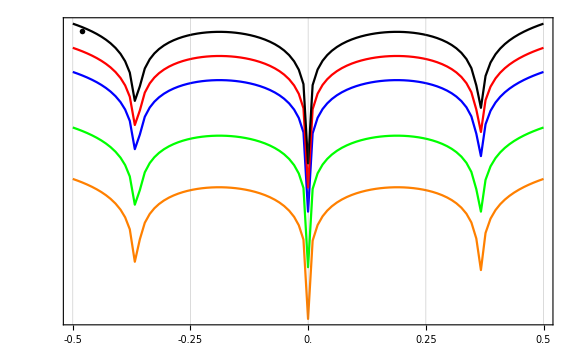

```mathematica
corrientePlotAntiBEAnotada = Show[corrientePlotAntiBE, FrameLabel->{{None,MaTeX["\\left\\langle \\hat{J} \\right\\rangle (\\mathrm{J}/\\mathrm{m}^{2}\\mathrm{s})", Magnification->1.8]},{
MaTeX["y/W", Magnification->1.8], None}
},GridLines->{{-0.5, -0.25,0,0.25, 0.5},Automatic},

Epilog->Inset[MaTeX["\\mathrm{f)}", Magnification->1.8],{-0.48,Log[3*10^5]}]]
```

```mathematica
meanSquareVelocitySimBE[y_,θ1_,θ2_]:=Sum[PlanckConstant/(densidad*largo*ancho*altura)*(amplitudWSim[2π*n*ancho/largo,y,0.0]^2*(frecuenciaωSimPositivo[2π*n*ancho/largo, 0.0]*ωRing))*(distribucionBE[frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing,θ1] +distribucionBE[frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing,θ2] +2),{n,1, 30}];
```

```mathematica
meanSquareVelocityAntiSimBE[y_,θ1_,θ2_]:=Sum[PlanckConstant/(densidad*largo*ancho*altura)*(amplitudWAntiSim[2π*n*ancho/largo,y]^2*(frecuenciaωAntiSimPositivo[2π*n*ancho/largo]*ωRing))*(distribucionBE[frecuenciaωAntiSimPositivo[2π*n*ancho/largo]*ωRing,θ1] +distribucionBE[frecuenciaωAntiSimPositivo[2π*n*ancho/largo]*ωRing,θ2] +2),{n,1, 30}];
```

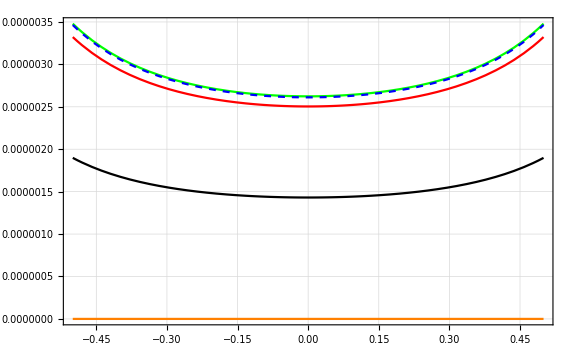

```mathematica
velocityPlotBE=Plot[{meanSquareVelocitySimBE[y,11.,10.99995],meanSquareVelocitySimBE[y,11.,10.9], meanSquareVelocitySimBE[y,11.,10.0],  meanSquareVelocitySimBE[y,11.,1.],meanSquareVelocitySimBE[y, 1*10^-4, 5*10^-5] },{y,-0.5,0.5}, PlotStyle->{Green,Directive[Blue, Dashed], Red, Black,Orange}, ImageSize->Large, GridLines->Automatic,MaxRecursion->1,
LabelStyle->{FontFamily->"CMU Serif", FontSize->18}, Frame->True,FrameStyle->Directive[Black, Thick]
]
```

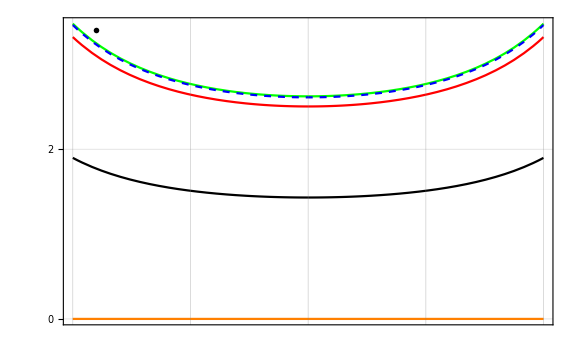

```mathematica
velocityPlotBEAnotada=Show[velocityPlotBE, FrameLabel->{{MaTeX["\\left\\langle \\hat{\\dot{\\xi}}^{2} \\right\\rangle (10^{-6} \\mathrm{m}/\\mathrm{s})", Magnification->1.8], None},{
None, None}
},GridLines->{{-0.5, -0.25,0,0.25, 0.5},Automatic},
FrameTicks->{
{Table[{j*10^-6,Style[ToString[j], Black]},{j,Range[0,10,1]}],False (*y axis*)},{Table[{j,""},{j,Range[-0.5,0.5,0.25]}](*x axis*),False}
},
Epilog->Inset[MaTeX["\\mathrm{c)}", Magnification->1.8],{-0.45,3.4*10^-6}]]
```

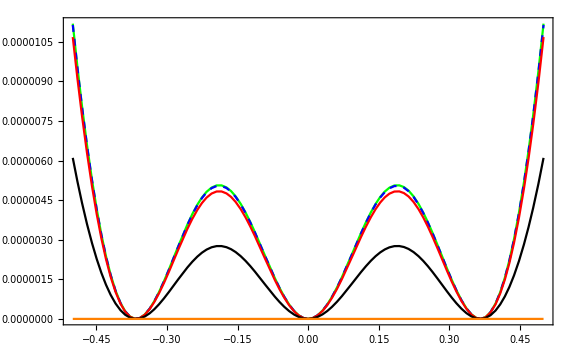

```mathematica
velocityPlotAntiBE=Plot[{meanSquareVelocityAntiSimBE[y,11.,10.99995],meanSquareVelocityAntiSimBE[y,11.,10.9], meanSquareVelocityAntiSimBE[y,11.,10.0],  meanSquareVelocityAntiSimBE[y,11.,1.],meanSquareVelocityAntiSimBE[y, 1*10^-4, 5*10^-5] },{y,-0.5,0.5}, PlotStyle->{Green,Directive[Blue, Dashed], Red, Black,Orange}, ImageSize->Large,MaxRecursion->1,
LabelStyle->{FontFamily->"CMU Serif", FontSize->18}, Frame->True,FrameStyle->Directive[Black, Thick]
]
```

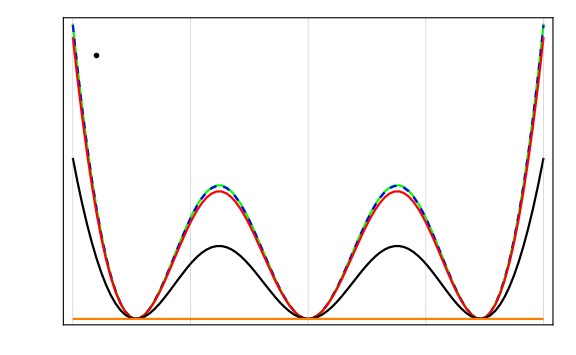

```mathematica
velocityPlotAntiBEAnotado=Show[velocityPlotAntiBE, FrameLabel->{{None,MaTeX["\\left\\langle \\hat{\\dot{\\xi}}^{2} \\right\\rangle (10^{-5} \\mathrm{m}/\\mathrm{s})", Magnification->1.8]},{
None, None}
},GridLines->{{-0.5, -0.25,0,0.25, 0.5},Automatic},
FrameTicks->{
{False,Table[{j*10^-5,Style[ToString[j], Black]},{j,Range[0,2,0.2]}](*y axis*)},{Table[{j,""},{j,Range[-0.5,0.5,0.25]}](*x axis*),False}
},
Epilog->Inset[MaTeX["\\mathrm{d)}", Magnification->1.8],{-0.45,1.*10^-5}]]
```

```mathematica
[{{msdSimBEAnotada, msdAntiSimBEAnotada},
{velocityPlotBEAnotada, velocityPlotAntiBEAnotado},
{corrientePlotBEAnotada, corrientePlotAntiBEAnotada}}, ImageSize->Full]
```

-Graphics-

```mathematica
Export["meanValuesBE.pdf",%]
```

meanValuesBE.pdf

```mathematica
conductanciaBE[y_,θ_]:=Sum[(PlanckConstant^2*velocidad^2)/(BoltzmannConstant*θ^2*largo)*(2π*n/largo)*frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing*amplitudWSim[2π*n*ancho/largo,y,0.0]^2* (Exp[(frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing*PlanckConstant)/(BoltzmannConstant*θ)]/(Exp[(frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing*PlanckConstant)/(BoltzmannConstant*θ)]-1)^2), {n, 1, 30}];
conductanciaAntiBE[y_,θ_]:=Sum[(PlanckConstant^2*velocidad^2)/(BoltzmannConstant*θ^2*largo)*(2π*n/largo)*frecuenciaωAntiSimPositivo[2π*n*ancho/largo]*ωRing*amplitudWAntiSim[2π*n*ancho/largo,y]^2* (Exp[(frecuenciaωAntiSimPositivo[2π*n*ancho/largo]*ωRing*PlanckConstant)/(BoltzmannConstant*θ)]/(Exp[(frecuenciaωAntiSimPositivo[2π*n*ancho/largo]*ωRing*PlanckConstant)/(BoltzmannConstant*θ)]-1)^2), {n, 1, 30}];
conductanciaIntegrada[θ_]:=(PlanckConstant^2*velocidad^2)/(BoltzmannConstant*θ^2*largo)*Sum[(2π*n/largo)*frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing* (Exp[(frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing*PlanckConstant)/(BoltzmannConstant*θ)]/(Exp[(frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing*PlanckConstant)/(BoltzmannConstant*θ)]-1)^2),{n,1,30}];
conductanciaIntegradaAnti[θ_]:=(PlanckConstant^2*velocidad^2)/(BoltzmannConstant*θ^2*largo)*Sum[(2π*n/largo)*frecuenciaωAntiSimPositivo[2π*n*ancho/largo]*ωRing* (Exp[(frecuenciaωAntiSimPositivo[2π*n*ancho/largo]*ωRing*PlanckConstant)/(BoltzmannConstant*θ)]/(Exp[(frecuenciaωAntiSimPositivo[2π*n*ancho/largo]*ωRing*PlanckConstant)/(BoltzmannConstant*θ)]-1)^2),{n,1,30}]
```

```mathematica
conductanciaBEInt[θ_]:=NIntegrate[conductanciaBE[y, θ],{y, -0.5, 0.5}];
conductanciaAntiBEInt[θ_]:=NIntegrate[conductanciaAntiBE[y,θ],{y, -0.5,0.5}]
```

```mathematica
conductanciaAntiBEInt[5]
conductanciaBEInt[5]
conductanciaIntegrada[10]
conductanciaIntegradaAnti[10]
```

9.55179×10^-10

1.97158×10^-8

1.97158×10^-8

9.55179×10^-10

General::munfl: 7.17757×10^167 1.94108821591944×10^-336 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.85724×10^168 2.89911225996684×10^-337 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 9.03137×10^168 1.22600583657399×10^-338 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

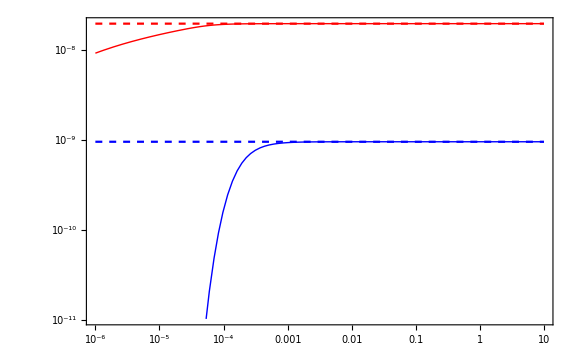

```mathematica
conductancePlotBE=LogLogPlot[{1.9715816728905868*^-8,9.551791428545576*^-10,conductanciaIntegrada[θ],conductanciaIntegradaAnti[θ] }, {θ, 0.000001, 10},PlotStyle->{Directive[Red, Dashed], Directive[Blue, Dashed],Directive[Red, Thick], Directive[Blue, Thick]},MaxRecursion->1, ImageSize->Large,PlotRange->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->18}, Frame->True,FrameStyle->Directive[Black, Thick],FrameTicks->{
{Table[{1*10^-j,("10")^ToString[Evaluate[9-j]]},{j,Range[5,11,1]}],False (*y axis*)},{Table[{1*10^-j,("10")^ToString[-j]},{j,Range[-1,10,1]}](*x axis*),False}
}

]
```

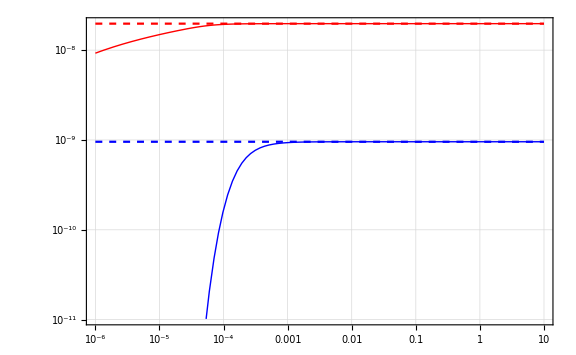

```mathematica
Show[conductancePlotBE,FrameLabel->{{MaTeX["\\mathcal{C} ( \\mu \\mathrm{W} / \\mathrm{K})", Magnification->2], None},{
MaTeX["T ( \\mathrm{K})", Magnification->2], None}
},GridLines->{Automatic,Automatic},LabelStyle->{FontFamily->"CMU Serif", FontSize->20},

Epilog->Inset[MaTeX["\\mathrm{c)}", Magnification->2],{-0.47,33*10^-6}]]
```

```mathematica
Export["conductance.pdf", %]
```

conductance.pdf